### Init

```mathematica
n=8;
g=GridGraph[{n,n}];
```

```mathematica
temperatureTable=Table[RandomReal[],n^2];

initialCircleCondition={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,2,2,2,2,0,0,0,0,2,2,2,2,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

hg1={{1,2},{1,9},{2,1},{2,3},{2,10},{3,2},{3,4},{3,11},{4,3},{4,5},{4,12},{5,4},{5,6},{5,13},{6,5},{6,7},{6,14},{7,6},{7,8},{7,15},{8,7},{8,16},{9,1},{9,10},{9,17},{10,2},{10,9},{10,11},{10,18},{11,3},{11,10},{11,12},{11,19},{12,4},{12,11},{12,13},{12,20},{13,5},{13,12},{13,14},{13,21},{14,6},{14,13},{14,15},{14,22},{15,7},{15,14},{15,16},{15,23},{16,8},{16,15},{16,24},{17,9},{17,18},{17,25},{18,10},{18,17},{18,19},{18,26},{19,11},{19,18},{19,20},{19,27},{20,12},{20,19},{20,21},{20,28},{21,13},{21,20},{21,22},{21,29},{22,14},{22,21},{22,23},{22,30},{23,15},{23,22},{23,24},{23,31},{24,16},{24,23},{24,32},{25,17},{25,26},{25,33},{26,18},{26,25},{26,27},{26,34},{27,19},{27,26},{27,28},{27,35},{28,20},{28,27},{28,29},{28,36},{29,21},{29,28},{29,30},{29,37},{30,22},{30,29},{30,31},{30,38},{31,23},{31,30},{31,32},{31,39},{32,24},{32,31},{32,40},{33,25},{33,34},{33,41},{34,26},{34,33},{34,35},{34,42},{35,27},{35,34},{35,36},{35,43},{36,28},{36,35},{36,37},{36,44},{37,29},{37,36},{37,38},{37,45},{38,30},{38,37},{38,39},{38,46},{39,31},{39,38},{39,40},{39,47},{40,32},{40,39},{40,48},{41,33},{41,42},{41,49},{42,34},{42,41},{42,43},{42,50},{43,35},{43,42},{43,44},{43,51},{44,36},{44,43},{44,45},{44,52},{45,37},{45,44},{45,46},{45,53},{46,38},{46,45},{46,47},{46,54},{47,39},{47,46},{47,48},{47,55},{48,40},{48,47},{48,56},{49,41},{49,50},{49,57},{50,42},{50,49},{50,51},{50,58},{51,43},{51,50},{51,52},{51,59},{52,44},{52,51},{52,53},{52,60},{53,45},{53,52},{53,54},{53,61},{54,46},{54,53},{54,55},{54,62},{55,47},{55,54},{55,56},{55,63},{56,48},{56,55},{56,64},{57,49},{57,58},{58,50},{58,57},{58,59},{59,51},{59,58},{59,60},{60,52},{60,59},{60,61},{61,53},{61,60},{61,62},{62,54},{62,61},{62,63},{63,55},{63,62},{63,64},{64,56},{64,63}};
```

```mathematica
k=0.1;δt=0.5;
```

```mathematica
ruleSet=ResourceFunction["EnumerateWolframModelRules"][{{2,2}}->{{2,2}}];
```

ResourceObject::updav: There is an update available for resource "ParallelMapMonitored". Use ResourceUpdate[ParallelMapMonitored] to get the update.

```mathematica
graphToHypergraphNew[g_]:=Flatten[DeleteCases[Table[If[(Normal@AdjacencyMatrix@g)[[#]][[i]]*i==0,0,{#,i}],{i,VertexList@g}],0]&/@(VertexList@g),1]

rwLaplacian[g_]:=IdentityMatrix[Length@VertexList@g]-Dot[Inverse@Normal@DiagonalMatrix[VertexOutDegree@g],Normal@AdjacencyMatrix[g]]

dynamicDiscreteLaplacian[G_,ϕ_]:=Dot[IdentityMatrix[Length@VertexList@G]-Dot[Inverse@Normal@DiagonalMatrix[VertexOutDegree@G],Normal@AdjacencyMatrix[G]],ϕ]

EulerMethod489[{HG_,t_,ϕ_}]:={ResourceFunction["WolframModel"][#,HG,1,"FinalState"]&[ruleSet[[489]]],t+δt,ϕ-k*δt *dynamicDiscreteLaplacian[ResourceFunction["HypergraphToGraph"]@HG,ϕ]} 


listEvolution[r_,InitialCondition_]:=NestWhileList[
ResourceFunction["WolframModel"][r,#1,1,"FinalState"]&,
InitialCondition,
(!IsomorphicGraphQ[SimpleGraph@Graph[UndirectedEdge@@@#1],SimpleGraph@Graph[UndirectedEdge@@@#2]]&&ResourceFunction["ConnectedHypergraphQ"][#1])& ,
2,100
]

EulerMethodStatic[{HG_,t_,ϕ_}]:={HG,t+δt,ϕ-k*δt *dynamicDiscreteLaplacian[ResourceFunction["HypergraphToGraph"]@HG,ϕ]} 

graphToHypergraph[G_]:=Module[{subsets=Subsets[#,{1}]&/@AdjacencyList@G },Flatten[Table[Append[ #,(VertexList@G)[[i]]]&/@subsets[[i]],{i,VertexCount@g}],1]]

hausdorffDimension489[HG_]:=Module[{rule=ruleSet[[489]]},ResourceFunction["WolframHausdorffDimension"][SimpleGraph[Graph[UndirectedEdge@@@#]],All,{1,1},"VertexMethod"->Mean]&/@listEvolution[rule,HG]]
```

### gifs

```mathematica
gif5=Module[{data=NestList[EulerMethod489,{hg1,0,initialCircleCondition},40]},Table[Graph[UndirectedEdge@@@ResourceFunction["HypergraphToGraph"]@data[[1,1]],
GraphLayout->{"GridEmbedding","Dimension"->{8,8}},
VertexStyle->Thread[Range[VertexCount@ResourceFunction["HypergraphToGraph"]@data[[i,1]]]->ColorData["TemperatureMap"]/@data[[i,3]]],
VertexSize->1,VertexLabels->None,EdgeStyle->Thickness[0]],{i,40}]]
```

## 3D grid

```mathematica
n = 4;
g3=GridGraph[{n,n,n}];
temperatureTable3=Table[RandomReal[],n^3];
```

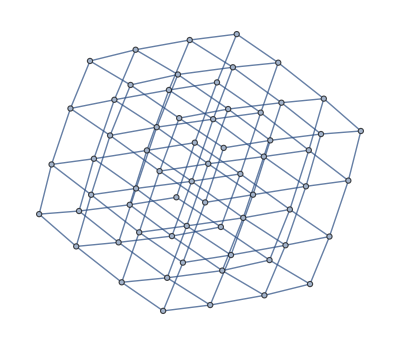

```mathematica
g3
```

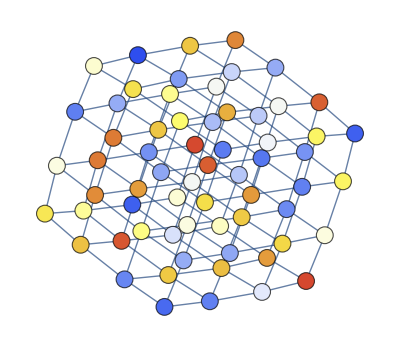

```mathematica
Graph[UndirectedEdge@@@g3, VertexStyle->Thread[Range[n^3]->ColorData["TemperatureMap"]/@temperatureTable3],VertexSize->1]
```

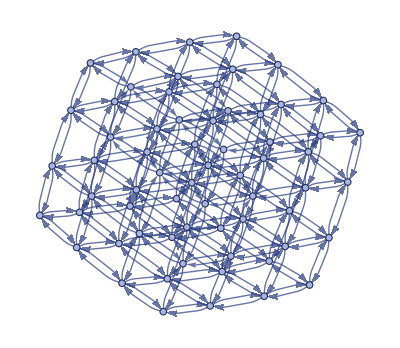

```mathematica
simpleGrid=ResourceFunction["WolframModelPlot"][graphToHypergraph@g3]
```

```mathematica
hg3 = graphToHypergraph@g3;
```

```mathematica
gif5=Module[{data=NestList[EulerMethod489,{hg3,0,temperatureTable3},40]},Table[Graph[UndirectedEdge@@@ResourceFunction["HypergraphToGraph"]@data[[i,1]],
VertexStyle->Thread[Range[VertexCount@ResourceFunction["HypergraphToGraph"]@data[[i,1]]]->ColorData["TemperatureMap"]/@data[[i,3]]],
VertexSize->1,VertexLabels->None,EdgeStyle->Thickness[0]],{i,40}]];
```

```mathematica
Export["3dDynamic.gif",gif5,"DisplayDurations"->0.2]
```

3dDynamic.gif

```mathematica
gif6=Module[{data=NestList[EulerMethod489,{hg3,0,temperatureTable3},40]},Table[Graph[UndirectedEdge@@@ResourceFunction["HypergraphToGraph"]@data[[1,1]],
VertexStyle->Thread[Range[VertexCount@ResourceFunction["HypergraphToGraph"]@data[[i,1]]]->ColorData["TemperatureMap"]/@data[[i,3]]],
VertexSize->1,VertexLabels->None,EdgeStyle->Thickness[0]],{i,40}]];
```

```mathematica
Export["3dDynamicFixedPosition.gif",gif6,"DisplayDurations"->0.2]
```

3dDynamicFixedPosition.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["3dDynamicFixedPosition.gif"]]]
```

```mathematica
p0=Variance/@NestList[EulerMethodStatic,{hg3,0,temperatureTable3},100][[All,3]];
p489=Variance/@NestList[EulerMethod489,{hg3,0,temperatureTable3},100][[All,3]];
```

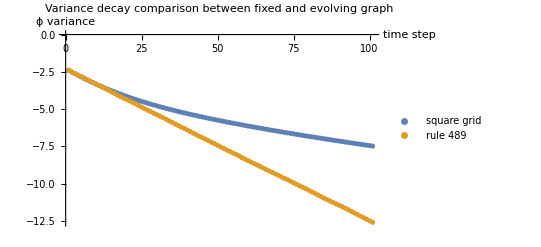

```mathematica
ListPlot[{Log@p0,Log@p489},PlotLabel->"Variance decay comparison between fixed and evolving graph",PlotLegends->{"square grid","rule 489"},PlotRange->All,AxesLabel->{"time step","ϕ variance"}]
```

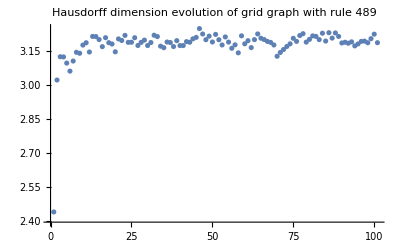

```mathematica
ListPlot[hausdorffDimension489[hg3],PlotRange->All,PlotLabel->"Hausdorff dimension evolution of grid graph with rule 489"]
```